```mathematica
δ[X_] = e*L*n/√(4π*D*t) Exp[-X^2 γ^2 Tan[ϕ]^2/(4*D*t)]
```

(e ⅇ^(-(X^2 γ^2 Tan[ϕ]^2)/(4 D t)) L n)/(2 √π √(D t))

```mathematica
X0 = Simplify[X/.Solve[D[δ[X],X] == -Tan[ϕ],X],{D>0,t>0,n>0,e>0,L>0,ϕ>0}][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(ⅈ √2 Cot[ϕ] √(D t ProductLog[-(8 D^2 π t^2)/(e^2 L^2 n^2 γ^2)]))/γ

```mathematica
FullSimplify[δ[X0]]
```

(e ⅇ^(1/2 ProductLog[-(8 D^2 π t^2)/(e^2 L^2 n^2 γ^2)]) L n)/(2 √π √(D t))

```mathematica
x[t_] = -X0/.{L->1.49,e->0.01129,n->0.065,ϕ->π/4,D->5.3*10^-10,γ->0.118}
ecart[t_] = 1-Exp[-x[t]^2 γ^2 Tan[ϕ]^2/(4*D*t)]/.{L->1.49,e->0.01129,n->0.065,ϕ->π/4,D->5.3*10^-10,γ->0.118}
```

(0.-0.000275912 ⅈ) √(t ProductLog[-4.24073×10^-10 t^2])

1-ⅇ^((0.5+0. ⅈ) ProductLog[-4.24073×10^-10 t^2])

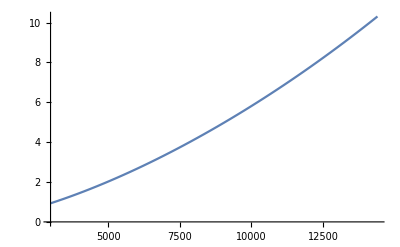

```mathematica
Plot[x[t]*1000,{t,49.9*60,4*3600}]
```

```mathematica
x[49.9*60]*1000
```

0.932604+0. ⅈ